```mathematica
ResourceFunction["MaTeXInstall"][];<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,graphicx}"}];
```

```mathematica
TexText[text_,m_]:=MaTeX[text,Magnification->m]
```

```mathematica
ClearAll[CuadrosDeColor,m]
Options[CuadrosDeColor]={m->2,legendMarkerSize->35,imgSize->80};
CuadrosDeColor[d_,OptionsPattern[]]:=Module[{labels},labels=Join[{TexText["1",OptionValue[m]]},Table[MaTeX["e^{2\\pi "<>ToString[i]<>"i/"<>ToString[d]<>"}" ,Magnification->OptionValue[m]],{i,1,d-1}]];SwatchLegend[ColorsOfGrid[d],labels,LegendMarkerSize->OptionValue[legendMarkerSize],ImageSize->OptionValue[imgSize]]
]
ColorsOfGrid[d_]:=Array[ColorData["DarkRainbow"],d,{0,1-1/d}]
```

```mathematica
CuadrosDeColor[3,m->2]
```

## Fig canales PCE

```mathematica
labelsS=MaTeX[#,FontSize->20]&/@{"1","0"};swatch=SwatchLegend[{RGBColor[0.237736, 0.340215, 0.575113],White},labelsS,LegendMarkerSize->25]
```

```mathematica
labels=Graphics[Table[indices=IntegerString[FromDigits[{m,n},4],2,4];Text[MaTeX["\\color{white}\\tau_{\\scalebox{.6}{"<>StringTake[indices,2]<>","<>StringTake[indices,-2]<>"}}",FontSize->34],{n+0.5,4-m-0.5}],{m,0,3},{n,0,3}],ImageSize->300];
```

```mathematica
PCEFigure[Taus_,literal_]:=Show[ArrayPlot[Taus,ColorRules->{1->RGBColor[0.237736, 0.340215, 0.575113],0->White},Frame->False,Mesh->True,MeshStyle->Directive[GrayLevel[.65],Thick],ImageSize->{300*1.1,300}],labels,Graphics[Text[MaTeX["(\\text{"<>ToString[literal]<>"})",FontSize->35],{-0.6,3.5}]]]
```

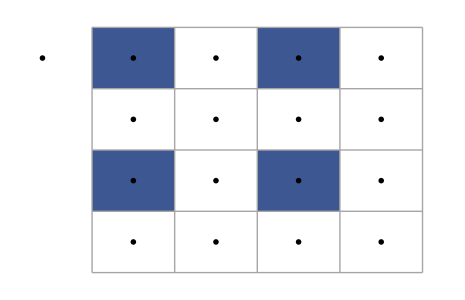

```mathematica
labelsS=MaTeX[#,FontSize->34]&/@{"1","0"};swatch=SwatchLegend[{RGBColor[0.237736, 0.340215, 0.575113],White},labelsS,LegendMarkerSize->45];

Show[PCEFigure[{{1,0,1,0},{0,0,0,0},{1,0,1,0},{0,0,0,0}},b],Graphics[Inset[swatch,{5.1,2}]],ImageSize->{300*1.55,300}]

Export[filename="/home/jadeleon/Documents/poster_cnf2023/pix/pce.pdf",%];

Run["pdfcrop "<>filename<>" "<>filename];
```

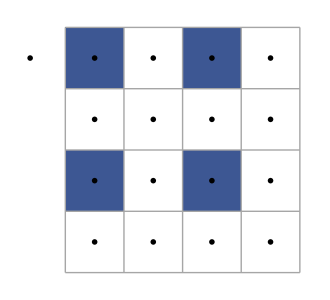

```mathematica
Show[PCEFigure[{{1,0,1,0},{0,0,0,0},{1,0,1,0},{0,0,0,0}},b],Graphics[Inset[swatch,{0,0}]]]

Export[filename="/home/jadeleon/Documents/poster_cnf2023/pix/pce.pdf",%];

Run["pdfcrop "<>filename<>" "<>filename];
```

```mathematica
r0={x0,y0,z0}={2.5,3,4};m=2;m1=1.5;TamañoFlecha=0.03;
sphere=Graphics3D[{Opacity[1],Arrowheads[{-TamañoFlecha,TamañoFlecha}],Arrow[{{-1,0,0},{1,0,0}}],Arrow[{{0,-1,0},{0,1,0}}],Opacity[0.5],Arrowheads[TamañoFlecha],Arrow[{{0,0,0},{0,0,1}}],Opacity[1],Arrow[{{0,0,0},{0,0,-1}}],Inset[MaTeX["\\boldsymbol{x}",Magnification->m],{1.1,0,0}],Inset[MaTeX["\\boldsymbol{y}",Magnification->m],{0,1.1,0}],Inset[MaTeX["\\boldsymbol{z}",Magnification->m],{0,0.08,0.93}]},
Boxed->False,ImageSize->400];

contour=ParametricPlot3D[{{Cos[t], Sin[t],0},{0, Cos[t], Sin[t]},{ Cos[t],0,Sin[t]}},{t,0,2 π},PlotStyle->ConstantArray[{Black,Dashed,Thickness[0.001]},3],Boxed->False,Axes->False,ImageSize->100];

f1=RegionPlot3D[Ellipsoid[{0,0,0},{1,1,1}],PlotStyle->Directive[Opacity[0.08],Orange,Specularity[White,5]],Boxed->False];

f2=RegionPlot3D[Ellipsoid[{0,0,0},{0.05,0.05,1}],PlotStyle->Directive[Opacity[0.25],Orange,Specularity[White,5]],Boxed->False];
f2=Graphics3D[{Opacity[.5],Orange,Specularity[White,5],Tube[{{0,0,-1},{0,0,1}},.018]}];

TamañoFlecha=0.03;

fig1=Show[sphere,contour,f1,f2,ViewPoint->{Pi,Pi/2,1.2}]

(*Export["/home/jadeleon/Documents/ja_master_thesis/gfx/ch1/phase_flip.pdf",%]*)
```

-Graphics3D-

```mathematica
r0={x0,y0,z0}={2.5,3,4};m=2;m1=1.5;TamañoFlecha=0.03;
sphere=Graphics3D[{Opacity[1],Arrowheads[{-TamañoFlecha,TamañoFlecha}],Arrow[{{-1,0,0},{1,0,0}}],Arrow[{{0,-1,0},{0,1,0}}],Opacity[0.5],Arrowheads[TamañoFlecha],Arrow[{{0,0,0},{0,0,1}}],Opacity[1],Arrow[{{0,0,0},{0,0,-1}}],Inset[MaTeX["\\boldsymbol{x}",Magnification->m],{1.1,0,0}],Inset[MaTeX["\\boldsymbol{y}",Magnification->m],{0,1.1,0}],Inset[MaTeX["\\boldsymbol{z}",Magnification->m],{0,0.08,0.93}]},
Boxed->False,ImageSize->400];

contour=ParametricPlot3D[{{Cos[t], Sin[t],0},{0, Cos[t], Sin[t]},{ Cos[t],0,Sin[t]}},{t,0,2 π},PlotStyle->ConstantArray[{Black,Dashed,Thickness[0.001]},3],Boxed->False,Axes->False,ImageSize->100];

f1=RegionPlot3D[Ellipsoid[{0,0,0},{1,1,1}],PlotStyle->Directive[Opacity[0.08],Orange,Specularity[White,5]],Boxed->False];

f2=RegionPlot3D[Ellipsoid[{0,0,0},{1,1,1}],PlotStyle->Directive[Opacity[0.25],Orange,Specularity[White,5]],Boxed->False];

TamañoFlecha=0.03;

fig2=Show[sphere,contour,f2,ViewPoint->{Pi,Pi/2,1.2}]

(*Export["/home/jadeleon/Documents/ja_master_thesis/gfx/ch1/identity.pdf",%]*)
```

-Graphics3D-

```mathematica
Show[GraphicsGrid[{{fig2,MaTeX["\\stackrel{\\text{PCE}}{\\mapsto}",Magnification->5],fig1}},ImageSize->{700,300},Spacings->{-160,0}],Graphics[Text[MaTeX["(\\text{"<>ToString[a]<>"})",FontSize->40],{-110,-50}]]]

Export[filename="/home/jadeleon/Documents/poster_cnf2023/pix/pce1qubit.pdf",%];

Run["pdfcrop "<>filename<>" "<>filename];
```

-Graphics-

```mathematica
Show[Graphics[Text[MaTeX["(\\text{"<>ToString[a]<>"})",FontSize->40],{-110,-50}]],GraphicsGrid[{{fig2,MaTeX["\\stackrel{\\text{PCE}}{\\mapsto}",Magnification->5],fig1}},ImageSize->{700,300},Spacings->{-160,0}],ImageSize->{700,300}]

Export[filename="/home/jadeleon/Documents/poster_cnf2023/pix/pce1qubit.pdf",%];

Run["pdfcrop "<>filename<>" "<>filename];
```

-Graphics-

```mathematica
r0={x0,y0,z0}={2.5,3,4};m=2;m1=1.5;
sphere=Graphics3D[{Opacity[1],Arrowheads[{-TamañoFlecha,TamañoFlecha}],Arrow[{{-1,0,0},{1,0,0}}],Arrow[{{0,-1,0},{0,1,0}}],Opacity[0.5],Arrowheads[TamañoFlecha],Arrow[{{0,0,0},{0,0,1}}],Opacity[1],Arrow[{{0,0,0},{0,0,-1}}],Inset[MaTeX["\\boldsymbol{x}",Magnification->m],{1.1,0,0}],Inset[MaTeX["\\boldsymbol{y}",Magnification->m],{0,1.1,0}],Inset[MaTeX["\\boldsymbol{z}",Magnification->m],{0,0.08,0.93}]},
Boxed->False,ImageSize->400];

contour=ParametricPlot3D[{{Cos[t], Sin[t],0},{0, Cos[t], Sin[t]},{ Cos[t],0,Sin[t]}},{t,0,2 π},PlotStyle->ConstantArray[{Black,Dashed,Thickness[0.001]},3],Boxed->False,Axes->False,ImageSize->100];

f1=RegionPlot3D[Ellipsoid[{0,0,0},{1,1,1}],PlotStyle->Directive[Opacity[0.08],Orange,Specularity[White,5]],Boxed->False];

f2=RegionPlot3D[Ellipsoid[{0,0,#},{√(1-#),√(1-#),1-#}]&[.85],PlotStyle->Directive[Opacity[0.25],Orange,Specularity[White,5]],Boxed->False];

TamañoFlecha=0.03;

phase=Show[sphere,contour,f1,f2,ViewPoint->{Pi,Pi/2,1.2}]
```

-Graphics3D-

```mathematica
GraphicsGrid[{{fig2,MaTeX["\\mapsto",Magnification->5],phase}},ImageSize->{700,300},Spacings->{-160,0}]

Export[filename="/home/jadeleon/Documents/poster_cnf2023/pix/phase_damping.pdf",%];

Run["pdfcrop "<>filename<>" "<>filename];
```

-Graphics-

## Fig

```mathematica
Import["/home/jadeleon/Documents/curiosidades/QuantumJA.wl"]
w[d_]:=ω[d]
w[d_,k_]:=Power[ω[d],k]
GridColorRules[d_]:=MapThread[Rule,{Table[w[d,i],{i,0,d-1}],Array[ColorData["DarkRainbow"],d,{0,1}]}]
GridColorRules[d_,1]:=MapThread[Rule,{Table[w[d,i],{i,0,d-1}],Array[ColorData["DarkRainbow"],d,{0,1-1/d}]}]
```

A::shdw: Symbol A appears in multiple contexts {QuantumJA`,Global`}; definitions in context QuantumJA` may shadow or be shadowed by other definitions.

```mathematica
WCEFigure[TauOfAWCEChannel_,imgSize:Except[1,_]:80]:=Module[{d=Sqrt[Length[TauOfAWCEChannel]]},ArrayPlot[ArrayReshape[TauOfAWCEChannel,{d,d}],ColorRules->GridColorRules[d],ImageSize->imgSize,Mesh->True]]
WCEFigure[TauOfAWCEChannel_,1,imgSize_:80]:=Module[{d=Sqrt[Length[TauOfAWCEChannel]]},ArrayPlot[ArrayReshape[TauOfAWCEChannel,{d,d}],ColorRules->GridColorRules[d,1],ImageSize->imgSize,Mesh->True,Frame->False,ImagePadding->0]]
WCEFigure[TauOfAWCEChannel_,2,imgSize_:80]:=Module[{d=Sqrt[Length[TauOfAWCEChannel]]},ArrayPlot[ArrayReshape[TauOfAWCEChannel,{d,d}],ColorRules->GridColorRules[d,1],ImageSize->imgSize,Mesh->False,Frame->False,ImagePadding->0]]
```

```mathematica
textoTaus=Graphics[Table[Text[MaTeX["\\color{white}\\tau_{\\scalebox{.5}{"<>ToString[Mod[m,4]]<>","<>ToString[Mod[n,4]]<>"}}",FontSize->20],{n+0.5,4-m-0.5}],{m,0,3},{n,0,3}],ImageSize->120];
```

```mathematica
claveColor=CuadrosDeColor[4,imgSize->95];
```

```mathematica
Show[WCEFigure[Flatten@DiagonalMatrix[{1,I,-1,-I}],1,120],textoTaus]
```

-Graphics-

```mathematica
textoTaus=Graphics[Table[Text[MaTeX["\\color{white}\\tau_{\\scalebox{.5}{"<>ToString[Mod[m,3]]<>","<>ToString[Mod[n,3]]<>"}}",FontSize->21],{n+0.5,3-m-0.5}],{m,0,2},{n,0,2}],ImageSize->120];
```

```mathematica
Show[WCEFigure[Flatten@DiagonalMatrix[{1,w[3],w[3,2]}],1,120],textoTaus]
```

-Graphics-

```mathematica
Clear[x,y,z]
Reduce[AllTrue[KroneckerProduct[#,Conjugate[#]]&[FourierMatrix[3]].{1,x I,-x I,y I,1,z I,-y I,-z I,1}//FullSimplify,#>=0&],{x,y,z}]
```

-1/(√3)≤x≤1/(√3)&&y==-x&&z==-y

```mathematica
1./(√3)
```

0.57735

```mathematica
{x,y,z}={0.5,-0.5,0.5}
AllTrue[KroneckerProduct[#,Conjugate[#]]&[FourierMatrix[3]].{1,x I,-x I,y I,1,z I,-y I,-z I,1}//FullSimplify,#>=0&]
```

{0.5,-0.5,0.5}

True

```mathematica
t={{Null,0.5I,-0.5I},{-0.5I,Null,0.5I},{0.5I,-0.5I,Null}}
```

{{Null,0.+0.5 ⅈ,0.-0.5 ⅈ},{0.-0.5 ⅈ,Null,0.+0.5 ⅈ},{0.+0.5 ⅈ,0.-0.5 ⅈ,Null}}

```mathematica
vals=Graphics[Table[If[t[[m+1,n+1]]===Null,Nothing,Text[MaTeX[ToString[Im@t[[m+1,n+1]]]<>"i",FontSize->14],{n+0.5,3-m-0.5}]],{m,0,2},{n,0,2}],ImageSize->120]
```

-Graphics-

```mathematica
Show[WCEFigure[Flatten@DiagonalMatrix[{1,w[3],w[3,2]}],1,120],textoTaus,vals]
```

-Graphics-

```mathematica
t={{Null,0.5I,-0.5I},{-0.5I,0.5I,Null},{0.5I,Null,-0.5I}};
vals=Graphics[Table[If[t[[m+1,n+1]]===Null,Nothing,Text[MaTeX[ToString[Im@t[[m+1,n+1]]]<>"i",FontSize->14],{n+0.5,3-m-0.5}]],{m,0,2},{n,0,2}],ImageSize->120]
```

-Graphics-

```mathematica
Show[WCEFigure[Flatten@{{1,0,0},{0,0,w[3,1]},{0,w[3,2],0}},1,120],textoTaus,vals]
```

-Graphics-

```mathematica
claveColor=CuadrosDeColor[3,imgSize->95]
```

```mathematica
labels=MaTeX[#,FontSize->20]&/@{"1","e^{2\\pi i/3}","e^{-2\\pi i/3}","0"};swatch=SwatchLegend[Join[ColorsOfGrid[3],{White}],labels,LegendMarkerSize->25]
```

```mathematica
GraphicsGrid[{{-Graphics-,-Graphics-}},Spacings->{30,0},Alignment->Left,ImageSize->280]
```

-Graphics-

```mathematica
GraphicsGrid[{{-Graphics-,swatch}},Alignment->Left,ImageSize->{480},Spacings->{25,0}]
```

-Graphics-

## Weyl erasing

```mathematica
labels=MaTeX[#,FontSize->15]&/@{"1","e^{2\\pi i/3}","e^{-2\\pi i/3}","0"};swatch=SwatchLegend[Join[ColorsOfGrid[3],{White}],labels,LegendMarkerSize->20]
```

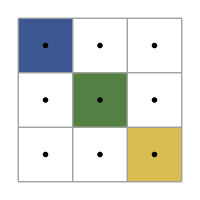
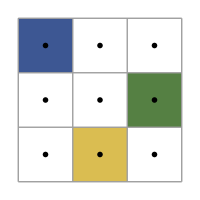
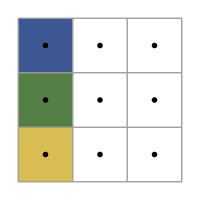

```mathematica
channels=Show[WCEFigure[Flatten@#,1,200],textoTaus]&/@{DiagonalMatrix[{1,w[3],w[3,2]}],{{1,0,0},{0,0,w[3,1]},{0,w[3,2],0}},{{1,0,0},{w[3,1],0,0},{w[3,2],0,0}}}
```

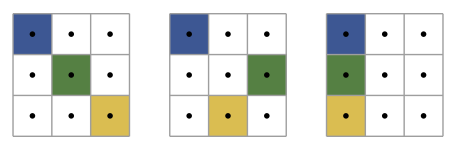

```mathematica
GraphicsGrid[{Join[channels,{swatch}]},ImageSize->{120*3.8,150},Spacings->{20,0},Alignment->Left]
```

## Fig de PCEs